# Lagaris Problem 3: 2nd-Order Linear ODE IVP and BVP

Solving the ODE in Mathematica:

```mathematica
de=ψ''[x]+1/5 ψ'[x]+ψ[x] == -1/5 ⅇ^(-x/5)Cos[x]
```

ψ[x]+ψ'[x]/5+ψ''[x]==-1/5 ⅇ^(-x/5) Cos[x]

```mathematica
generalSolution=FullSimplify[DSolve[de,ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) (Sin[x]+ⅇ^(x/10) (C[2] Cos[(3 √11 x)/10]+C[1] Sin[(3 √11 x)/10]))}}

```mathematica
particularSolution=FullSimplify[DSolve[{de,ψ[0]==0,ψ'[0]==1},ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) Sin[x]}}

```mathematica
ψa[x_]:=ψ[x]/.particularSolution[[1]]
```

Compute the derivatives of the solution.

```mathematica
FullSimplify[D[ψa[x],x]]
```

1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])

```mathematica
FullSimplify[D[ψa[x],{x,2}]]
```

-2/25 ⅇ^(-x/5) (5 Cos[x]+12 Sin[x])

```mathematica
dψadx[x_]:=1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])
```

```mathematica
d2ψadx2[x_]:=-2/25 ⅇ^(-x/5) (5 Cos[x]+12 Sin[x])
```

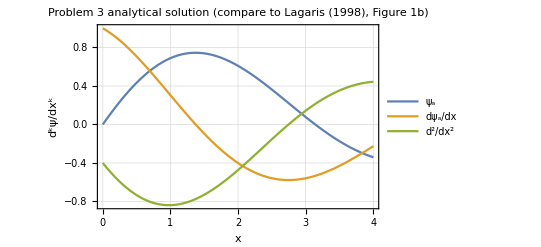

```mathematica
Plot[{ψa[x],dψadx[x],d2ψadx2[x]},{x,0,4},AxesLabel->{"x","d^kψ/dx^k"},PlotLegends->{"ψ_a","dψ_a/dx","d^2/dx^2"},PlotLabel->"Problem 3 analytical solution (compare to Lagaris (1998), Figure 1b)",Frame->True,GridLines->Automatic]
```